P. Huft
My notebook for converting the H.-L. eqs. for an atom interacting with a propagating quantized electric field into the Linblad form with the density operator. See the paper by Scarani.

## definitions

```mathematica
(*the Schrodinger picture operators, or equivalently the Heisenberg ops at t=t0*)
σ0=PauliMatrix[0];
σx=PauliMatrix[1];
σy=PauliMatrix[2];
σz=PauliMatrix[3];
σp=1/2(σx+I σy);
σm=1/2(σx-I σy);
a=σm;
adag=σp;
dag[z_]=ConjugateTranspose[z];

BuildMasterEq[ρ0_,H_, Llist_,t0_:0]:=Module[{dim,rho,eqIdcs,comm,linblad,rhoPruned,eqsPruned,rhoICPruned, popIdxList, cohIdxList, i, j,m,L},
(*The code below builds the equations to be passed to NDSolve, removing the redundant equations (since Subscript[ρ, ij]=Subscript[ρ, ji]^*).

"Pruned" variables refer to the eqs which have had the redundant elements removed.

Args: 
 ρ0: the initial density matrix;
	H: the Hamiltonian;
	L: the jump operators. I assume that decay constants γ are accounted for in L, which is to say that the Linblad term looks like (L ρ L^†-1/2(ρ L^†L +L^†L ρ)) rather than γ(L ρ L^†-1/2(ρ L^†L +L^†L ρ));
	t0: the initial time, which is 0 if not specified.

Returns: eqsPruned, rhoICPruned (the pruned initial state), rhoPruned (the pruned set of variables, i.e. elements of ρ, to solve for), popIdxList (the indices of the population terms), cohIdxList (inds of the coherence terms)
*)
Clear[ρ,t];
dim = Length[H];
rho=Array[Subscript[ρ, #1,#2][t]&,{dim,dim}];
(*enforce conjugate relationship of ρ's off-diagonals *)
eqIdcs = {};
For[i=1,i<dim+1,i++,
For[j=dim,j>i,j--,
rho[[j,i]] = Conjugate[rho[[i,j]]];
AppendTo[eqIdcs,{i,j}]
]
];
(*generate non-redundant eqs and initial conditions*)
comm =  H.rho-rho.H  ;
linblad=Array[0&,{dim,dim}];
For[m=1,m<Length[Llist]+1,m++,
L=Llist[[m]];
linblad +=L.rho.dag[L]-1/2(dag[L].L.rho + rho.dag[L].L);
];
(*linblad =L.rho.dag[L]-1/2(dag[L].L.rho + rho.dag[L].L);*)
rhoPruned ={};
eqsPruned = {};
rhoICPruned = {};
For[i=1,i<dim+1,i++,
For[j=1,j<dim+1,j++,
If[i<=j,
AppendTo[eqsPruned,D[rho[[i,j]],t]==-I comm[[i,j]]+linblad[[i,j]]];
AppendTo[rhoICPruned,(rho/.t-> t0)[[i,j]]==ρ0[[i,j]]];
AppendTo[rhoPruned,rho[[i,j]]];
(*Print[eqsPruned[[-1]]]*)
];
];
];
(*generate indices for population and coherence terms in pruned eq list*)
popIdxList ={1};
cohIdxList = {};
j=0;
last = 1;
elems = dim(dim+1)/2;
For[i=1,i<elems+1,i++,
If[i ==last+dim-j,
{AppendTo[popIdxList,i],last=i,j++},
AppendTo[cohIdxList,i]
]
];
{eqsPruned,rhoICPruned,rhoPruned, popIdxList, cohIdxList}
];
```

## Heisenberg-Langevin eqs

```mathematica
(*operators in the atom-field space with the Fock state basis truncated at N=1*)
aa=KroneckerProduct[a,σ0];
sm=KroneckerProduct[σ0,σm];
sp=dag[sm];
sz=KroneckerProduct[σ0,σz];
II=KroneckerProduct[σ0,σ0];
```

```mathematica
"sz dot"
szdot=-Γ(sz+II)-2g(sp.aa+sm.dag[aa]);
szdot//MatrixForm
"sm dot"
smdot=-Γ/2 sm+g sz.aa;
smdot//MatrixForm
"sp dot"
spdot=-Γ/2 sp+g dag[sz].dag[aa];
spdot//MatrixForm
```

sz dot

(-2 Γ | 0 | 0 | 0
0 | 0 | -2 g | 0
0 | -2 g | -2 Γ | 0
0 | 0 | 0 | 0)

sm dot

(0 | 0 | 0 | 0
-Γ/2 | 0 | 0 | 0
g | 0 | 0 | 0
0 | -g | -Γ/2 | 0)

sp dot

(0 | -Γ/2 | g | 0
0 | 0 | 0 | -g
0 | 0 | 0 | -Γ/2
0 | 0 | 0 | 0)

```mathematica
M=({{-Γ, -2g, -2g}, {0, -Γ/2, 0}, {0, 0, -Γ/2}});
b=({{-Γ}, {-g}, {-g}});
s=({{s1}, {s2}, {s3}});
s0=({{1}, {0}, {0}});
M.s+b//MatrixForm
```

(-2 g s2-2 g s3-Γ-s1 Γ
-g-(s2 Γ)/2
-g-(s3 Γ)/2)

## comparison with Linblad form

Do this by comparison of the form of the operator equations and the general form of the Linblad equation for an operator A:

ρ̇=-I/ℏ[H,ρ]+(L ρ L^†-1/2(ρ L^†L +L^†L ρ)) 

Ȧ=+I/ℏ[H,A]+(L^† A L-1/2(A L^†L +L^†L A)) 

The above equations are from https://en.wikipedia.org/wiki/Lindbladian, modified to have only one jump operator L and the assumption that the decay rate γ is accounted for in L itself. I checked that these are in agreement with John Preskill's quantum info notes (https://web.archive.org/web/20200623204052/http://www.theory.caltech.edu/people/preskill/ph219/chap3_15.pdf).

```mathematica
szdot//MatrixForm
```

(-2 Γ | 0 | 0 | 0
0 | 0 | -2 g | 0
0 | -2 g | -2 Γ | 0
0 | 0 | 0 | 0)

```mathematica
smdot//MatrixForm
```

(0 | 0 | 0 | 0
-Γ/2 | 0 | 0 | 0
g | 0 | 0 | 0
0 | -g | -Γ/2 | 0)

```mathematica
Clear[k1,k2,Γ,g]
H0=I g(-sp.aa+ sm.dag[aa]);
L0=k1 sm +k2 sz;(*depolarizing and dephasing*)
k2=0;
k1=√Γ;
"sz dot with H,L guesses"
Refine[I (H0.sz-sz.H0)+(dag[L0].sz.L0-1/2(dag[L0].L0.sz+sz.dag[L0].L0)),Γ>0]//MatrixForm//TraditionalForm
"correct sz dot"
szdot//MatrixForm
```

sz dot with H,L guesses

(-2 Γ | 0 | 0 | 0
0 | 0 | -2 g | 0
0 | -2 g | -2 Γ | 0
0 | 0 | 0 | 0)

correct sz dot

(-2 Γ | 0 | 0 | 0
0 | 0 | -2 g | 0
0 | -2 g | -2 Γ | 0
0 | 0 | 0 | 0)

```mathematica
"sm dot with H,L guesses"
Refine[I (H0.sm-sm.H0)+(dag[L0].sm.L0-1/2(dag[L0].L0.sm+sm.dag[L0].L0)),Γ>0]//MatrixForm//TraditionalForm
"correct sm dot"
smdot//MatrixForm
```

sm dot with H,L guesses

(0 | 0 | 0 | 0
-Γ/2 | 0 | 0 | 0
g | 0 | 0 | 0
0 | -g | -Γ/2 | 0)

correct sm dot

(0 | 0 | 0 | 0
-Γ/2 | 0 | 0 | 0
g | 0 | 0 | 0
0 | -g | -Γ/2 | 0)

## simulate H.-L. equations

See Scarani. This reproduces Fig. 1, as a sanity check. The equations below describe the evolution of the expectation values of the atomic operators σz, σ+, σ- (see Scarani for the states used), which are labeled s1, s2, s3. This does not solve for the evolution of the operators themselves.

Time to run sim step 1: 0.03125

Time to run sim step 2: 0.015625

Time to run sim step 3: 0.

Time to run sim step 4: 0.015625

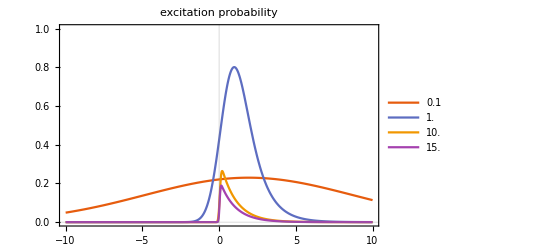

General::munfl: Exp[-5624.54] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12655.2] is too small to represent as a normalized machine number; precision may be lost.

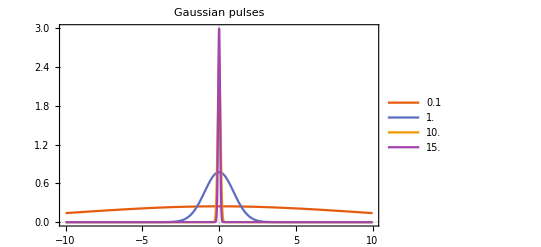

```mathematica
tmin=-100;
tmax=10;
Clear[s,M,b,t]
Γ=1;
Γp=Γ;
Ω0=1.5Γ;
Ωarr={0.1,1,10, 15}Ω0;
PeArr={};
PulseArr={};
For[i=1,i<Length[Ωarr]+1,i++,
Ω=Ωarr[[i]];
g[t]=√Γp(Ω^2/(2π))^(1/4)Exp[-(Ω t)^2/4];
AppendTo[PulseArr, g[t]];
M=({{-Γ, -2g[t], -2g[t]}, {0, -Γ/2, 0}, {0, 0, -Γ/2}});
b=({{-Γ}, {-g[t]}, {-g[t]}});
s=({{s1[t]}, {s2[t]}, {s3[t]}});
eqs=Array[(D[s,t]-(M.s+b))[[#,1]]==0&,3];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,{s1[tmin]==1,s2[tmin]==0,s3[tmin]==0}], s, {t,tmin,tmax}, MaxStepFraction->1/1000]];
Print["Time to run sim step ",i,": ",time];
Pe=1/2(soln[[1,2]]+1);
AppendTo[PeArr,Pe];
]

Plot[PeArr,{t,-10,10},PlotLegends->Ωarr/Ω0,PlotLabel->"excitation probability",PlotRange->{{-10,10},{0,1}},PlotTheme->"Scientific"]
Plot[PulseArr,{t,-10,10},PlotLegends->Ωarr/Ω0,PlotLabel->"Gaussian pulses",PlotRange->All,PlotTheme->"Scientific"]
```

## simulate Linblad eq. for Heisenberg operators

Reproduce Fig. 1, but by solving the Linbald equation for the time evolution of the operators and then measuring the expectation values of the operators using <A> = Tr[A(t) ρ] where ρ is fixed in time to be the initial state. Apparently I’ve done this incorrectly, because the results do not agree with the expectation value simulation above.

```mathematica
sm//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0)

```mathematica
sz//MatrixForm
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
tmin=-100;
tmax=10;
t0=0;

Γ=1;
Γp=Γ;
Ω0=1.5Γ;
Ωarr={0.1,1,10,15}Ω0;

(*substates kets and density matrices*)
ψatomg={1,0};(*{g,e}*)
ψatome={0,1};(*{g,e}*)
ψfield0={1,0};(*{0,1}*)
ψfield1={0,1};(*{0,1}*)
ρg = Outer[Times,ψatomg,ψatomg];
ρe = Outer[Times,ψatome,ψatome];
ρf0 = Outer[Times,ψfield0,ψfield0];
ρf1= Outer[Times,ψfield1,ψfield1];

(*population projectors*)
"atom g, field 0"
ρ00=KroneckerProduct[ρg,ρf0];
ρ00//MatrixForm
"atom g, field 1"
ρ01=KroneckerProduct[ρg,ρf1];
ρ01//MatrixForm
"atom e, field 0"
ρ10=KroneckerProduct[ρe,ρf0];
ρ10//MatrixForm
"atom e, field 1"
ρ11=KroneckerProduct[ρe,ρf1];
ρ11//MatrixForm

(*initial state*)
ρ0=KroneckerProduct[ρg,ρf1];
```

atom g, field 0

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

atom g, field 1

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

atom e, field 0

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)

atom e, field 1

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
Clear[H,L,t,Sz,Sm,SZ,SM]
SZsolnList={};
SMsolnList={};
PulseArr={};
For[k=1,k<Length[Ωarr]+1,k++,
Ω=Ωarr[[k]];

g=√Γp(Ω^2/(2π))^(1/4)Exp[-(Ω (t-t0))^2/4];
AppendTo[PulseArr, g];

SZinitial={};
SMinitial={};
SZ=Array[Subscript[Sz, #1,#2][t]&,{4,4}];
SM=Array[Subscript[Sm, #1,#2][t]&,{4,4}];

(*RWA interaction Hamiltonian-- ignore dc terms for field and atom b.c. there is no detuning here*)
H=ⅈ g(-ConjugateTranspose[SM].aa+ SM.dag[aa]);

(*decay operator for atom excited state*)
L=√Γ SM;

variables=Join[Flatten@SM,Flatten@SZ];
(*the Heisenberg operators are equivalent to the Schrodinger picture ones at the start time*)
For[i=1,i<5,i++,
For[j=1,j<5,j++,
(*the Heisenberg operators are equivalent to the Schrodinger picture ones at the start time*)
AppendTo[SZinitial,Subscript[Sz, i,j][tmin]==sz[[i,j]]];
];
];
For[i=1,i<5,i++,
For[j=1,j<5,j++,
AppendTo[SMinitial,Subscript[Sm, i,j][tmin]==sm[[i,j]]];
];
];
initialConditions=Join@{SZinitial,SMinitial};

SZdot=ⅈ (H.SZ-SZ.H)+(dag[L].SZ.L-1/2(dag[L].L.SZ+SZ.dag[L].L));
SMdot=ⅈ (H.SM-SM.H)+(dag[L].SM.L-1/2(dag[L].L.SM+SM.dag[L].L));
eqs={};
For[i=1,i<5,i++,
For[j=1,j<5,j++,
AppendTo[eqs,D[Subscript[Sz, i,j][t],t]==SZdot[[i,j]]];
AppendTo[eqs,D[Subscript[Sm, i,j][t],t]==SMdot[[i,j]]];
];
];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,initialConditions], variables, {t,tmin,tmax}, MaxStepFraction->1/10000]];
Print["Time to run sim step ",k,": ",time];
AppendTo[SZsolnList,ArrayReshape[soln[[17;;]],{4,4}]];
AppendTo[SMsolnList,ArrayReshape[soln[[;;16]],{4,4}]];
]
```

Time to run sim step 1: 0.421875

Time to run sim step 2: 0.46875

Time to run sim step 3: 0.453125

Time to run sim step 4: 0.453125

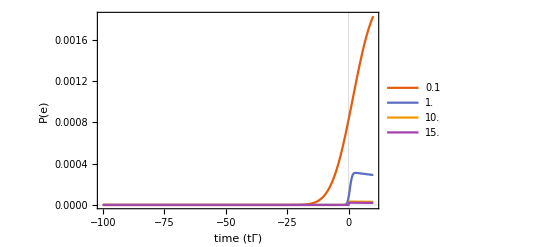

```mathematica
(*this should reproduce the curves of the operator expectation values shown above, but does not*)
ρ=ρ0;
Plot[Evaluate[Array[1/2(Tr[Values[SZsolnList[[#]]].ρ]+1)&,4]],{t,tmin,tmax},PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"time (tΓ)","P(e)"},PlotLegends->Ωarr/Ω0]
```

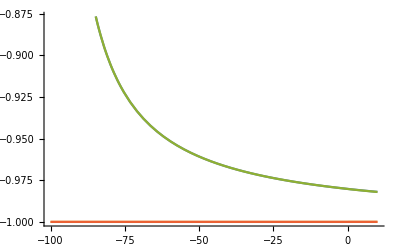

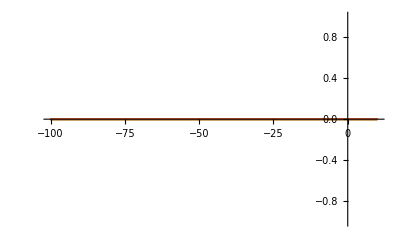

```mathematica
idx=4;
Plot[Evaluate[{Tr[Values[SZsolnList[[idx]]].ρ00],Tr[Values[SZsolnList[[idx]]].ρ01],Tr[Values[SZsolnList[[idx]]].ρ10],Tr[Values[SZsolnList[[idx]]].ρ11]}],{t,tmin,tmax}]
Plot[Evaluate[{Tr[Values[SMsolnList[[idx]]].ρ00],Tr[Values[SMsolnList[[idx]]].ρ01],Tr[Values[SMsolnList[[idx]]].ρ10],Tr[Values[SMsolnList[[idx]]].ρ11]}],{t,tmin,tmax}]
```

```mathematica
Values[SZsolnList[[1]]]//MatrixForm
```

(InterpolatingFunction[…][t] | InterpolatingFunction[…][t] | InterpolatingFunction[…][t] | InterpolatingFunction[…][t]
InterpolatingFunction[…][t] | InterpolatingFunction[…][t] | InterpolatingFunction[…][t] | InterpolatingFunction[…][t]
InterpolatingFunction[…][t] | InterpolatingFunction[…][t] | InterpolatingFunction[…][t] | InterpolatingFunction[…][t]
InterpolatingFunction[…][t] | InterpolatingFunction[…][t] | InterpolatingFunction[…][t] | InterpolatingFunction[…][t])

```mathematica
SMinitial
```

{Sm_(1,1)[-100]==0,Sm_(1,2)[-100]==0,Sm_(1,3)[-100]==0,Sm_(1,4)[-100]==0,Sm_(2,1)[-100]==1,Sm_(2,2)[-100]==0,Sm_(2,3)[-100]==0,Sm_(2,4)[-100]==0,Sm_(3,1)[-100]==0,Sm_(3,2)[-100]==0,Sm_(3,3)[-100]==0,Sm_(3,4)[-100]==0,Sm_(4,1)[-100]==0,Sm_(4,2)[-100]==0,Sm_(4,3)[-100]==1,Sm_(4,4)[-100]==0}

```mathematica
SZinitial
```

{Sz_(1,1)[-100]==1,Sz_(1,2)[-100]==0,Sz_(1,3)[-100]==0,Sz_(1,4)[-100]==0,Sz_(2,1)[-100]==0,Sz_(2,2)[-100]==-1,Sz_(2,3)[-100]==0,Sz_(2,4)[-100]==0,Sz_(3,1)[-100]==0,Sz_(3,2)[-100]==0,Sz_(3,3)[-100]==1,Sz_(3,4)[-100]==0,Sz_(4,1)[-100]==0,Sz_(4,2)[-100]==0,Sz_(4,3)[-100]==0,Sz_(4,4)[-100]==-1}

```mathematica
Tr[ρ00.Values[SZsolnList[[1]]]]/.t->tmin//MatrixForm
```

1.

```mathematica
Tr[Values[SZsolnList[[1]]].ρ00]/.t->tmin+1
Tr[Values[SZsolnList[[1]]].ρ00]/.t->tmin+2
Tr[Values[SZsolnList[[1]]].ρ00]/.t->tmin+3
Tr[Values[SZsolnList[[1]]].ρ00]/.t->tmin+4
```

3.49579×10^-8

-0.333333

-0.5

-0.6

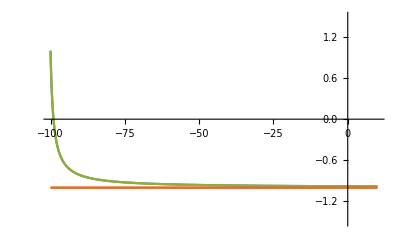

```mathematica
Plot[{Tr[Values[SZsolnList[[1]]].ρ00],Tr[Values[SZsolnList[[1]]].ρ01],Tr[Values[SZsolnList[[1]]].ρ10],Tr[Values[SZsolnList[[1]]].ρ11]},{t,tmin,tmax},PlotRange->{{tmin,tmax},{-1.5,1.5}}]
```

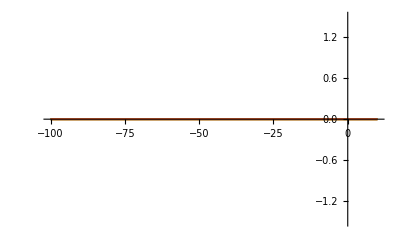

```mathematica
Plot[{Tr[Values[SMsolnList[[1]]].ρ00],Tr[Values[SMsolnList[[1]]].ρ01],Tr[Values[SMsolnList[[1]]].ρ10],Tr[Values[SMsolnList[[1]]].ρ11]},{t,tmin,tmax},PlotRange->{{tmin,tmax},{-1.5,1.5}}]
```

```mathematica
Values[SZsolnList[[1]]].ρ0/.t->0.1//MatrixForm
```

(0 | 0. | 0 | 0
0 | -1. | 0 | 0
0 | -1.93424×10^-15 | 0 | 0
0 | 0. | 0 | 0)

```mathematica
ArrayReshape[{1,2,3,4},{2,2}]
```

{{1,2},{3,4}}

```mathematica
SZsolnList[[]]
```

```mathematica
Tr[ρ00.solnList[[1]]]
```

{Sm_(1,1)[t]->InterpolatingFunction[…][t],Sm_(1,2)[t]->InterpolatingFunction[…][t],Sm_(1,3)[t]->InterpolatingFunction[…][t],Sm_(1,4)[t]->InterpolatingFunction[…][t],Sm_(2,1)[t]->InterpolatingFunction[…][t],Sm_(2,2)[t]->InterpolatingFunction[…][t],Sm_(2,3)[t]->InterpolatingFunction[…][t],Sm_(2,4)[t]->InterpolatingFunction[…][t],Sm_(3,1)[t]->InterpolatingFunction[…][t],Sm_(3,2)[t]->InterpolatingFunction[…][t],Sm_(3,3)[t]->InterpolatingFunction[…][t],Sm_(3,4)[t]->InterpolatingFunction[…][t],Sm_(4,1)[t]->InterpolatingFunction[…][t],Sm_(4,2)[t]->InterpolatingFunction[…][t],Sm_(4,3)[t]->InterpolatingFunction[…][t],Sm_(4,4)[t]->InterpolatingFunction[…][t],Sz_(1,1)[t]->InterpolatingFunction[…][t],Sz_(1,2)[t]->InterpolatingFunction[…][t],Sz_(1,3)[t]->InterpolatingFunction[…][t],Sz_(1,4)[t]->InterpolatingFunction[…][t],Sz_(2,1)[t]->InterpolatingFunction[…][t],Sz_(2,2)[t]->InterpolatingFunction[…][t],Sz_(2,3)[t]->InterpolatingFunction[…][t],Sz_(2,4)[t]->InterpolatingFunction[…][t],Sz_(3,1)[t]->InterpolatingFunction[…][t],Sz_(3,2)[t]->InterpolatingFunction[…][t],Sz_(3,3)[t]->InterpolatingFunction[…][t],Sz_(3,4)[t]->InterpolatingFunction[…][t],Sz_(4,1)[t]->InterpolatingFunction[…][t],Sz_(4,2)[t]->InterpolatingFunction[…][t],Sz_(4,3)[t]->InterpolatingFunction[…][t],Sz_(4,4)[t]->InterpolatingFunction[…][t]}

```mathematica
SZ//MatrixForm
```

(Sz_(1,1)[t] | Sz_(1,2)[t] | Sz_(1,3)[t] | Sz_(1,4)[t]
Sz_(2,1)[t] | Sz_(2,2)[t] | Sz_(2,3)[t] | Sz_(2,4)[t]
Sz_(3,1)[t] | Sz_(3,2)[t] | Sz_(3,3)[t] | Sz_(3,4)[t]
Sz_(4,1)[t] | Sz_(4,2)[t] | Sz_(4,3)[t] | Sz_(4,4)[t])

```mathematica
variables
```

{Sm_(1,1)[t],Sm_(1,2)[t],Sm_(1,3)[t],Sm_(1,4)[t],Sm_(2,1)[t],Sm_(2,2)[t],Sm_(2,3)[t],Sm_(2,4)[t],Sm_(3,1)[t],Sm_(3,2)[t],Sm_(3,3)[t],Sm_(3,4)[t],Sm_(4,1)[t],Sm_(4,2)[t],Sm_(4,3)[t],Sm_(4,4)[t],Sm_(1,1)[t],Sm_(1,2)[t],Sm_(1,3)[t],Sm_(1,4)[t],Sm_(2,1)[t],Sm_(2,2)[t],Sm_(2,3)[t],Sm_(2,4)[t],Sm_(3,1)[t],Sm_(3,2)[t],Sm_(3,3)[t],Sm_(3,4)[t],Sm_(4,1)[t],Sm_(4,2)[t],Sm_(4,3)[t],Sm_(4,4)[t]}

### testing - compare ρ eqs with s eqs

```mathematica
M=({{-Γ, -2g, -2g}, {0, -Γ/2, 0}, {0, 0, -Γ/2}});
b=({{-Γ}, {-g}, {-g}});
s=({{s1}, {s2}, {s3}});
s0=({{1}, {0}, {0}});
M.s+b//MatrixForm
```

(-2 g s2-2 g s3-Γ-s1 Γ
-g-(s2 Γ)/2
-g-(s3 Γ)/2)

```mathematica
H=I g(-sp.aa+ sm.dag[aa]);
L=√Γ sm;

{eqs,initialConditions, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H, L, tmin];
Refine[eqs,Γ>0]//Simplify//MatrixForm//TraditionalForm
```

(Γ ρ_(1,1)(t)+ρ_(1,1)'(t)==0
Γ ρ_(1,2)(t)+2 ρ_(1,2)'(t)==2 g ρ_(1,3)(t)
g ρ_(1,2)(t)+Γ ρ_(1,3)(t)+ρ_(1,3)'(t)==0
Γ ρ_(1,4)(t)+2 ρ_(1,4)'(t)==0
g Conjugate[ρ_(2,3)(t)]+g ρ_(2,3)(t)+Γ ρ_(1,1)(t)==ρ_(2,2)'(t)
g ρ_(2,2)(t)+1/2 Γ ρ_(2,3)(t)+ρ_(2,3)'(t)==g ρ_(3,3)(t)
g ρ_(3,4)(t)+Γ ρ_(1,3)(t)==ρ_(2,4)'(t)
g Conjugate[ρ_(2,3)(t)]+g ρ_(2,3)(t)+Γ ρ_(3,3)(t)+ρ_(3,3)'(t)==0
2 g ρ_(2,4)(t)+Γ ρ_(3,4)(t)+2 ρ_(3,4)'(t)==0
Γ ρ_(3,3)(t)==ρ_(4,4)'(t))

## simulate Linblad density matrix eq.

Reproduce Fig. 1, but by solving the density matrix equation.  For high-bandwidth (temporally short) pulses, this agrees with the simulation of the s state from the Heisenberg-Langevin equations above, but they do not agree for longer duration pulses.  With no free energy terms for the field and the atom, the interaction and Schrodinger pictures coincide. However, perhaps I need to account for the energies, since the states are not all degenerate even at zero detuning: atom in g and field in 0 is not degenerate with atom in e, field in 0, and so on.

### ignore free energy of the atom, field

In this case, the interaction and Schrodinger picture Hamiltonians and states coincide.

```mathematica
tmin=-100;
tmax=10;
t0=0;
(*tmin=0;
tmax=110;
t0=100;*) (*the photon envelope is centered at t0*)

Γ=1;
Γp=Γ;
Ω0=1.5Γ;
Ωarr={0.1,1,10,15}Ω0;

(*basis kets*)
ψatomgfield0=Outer[Times,{1,0},{1,0}];
ψatomgfield1=Outer[Times,{1,0},{0,1}];
ψatomefield0=Outer[Times,{0,1},{1,0}];
ψatomefield1=Outer[Times,{0,1},{0,1}];

(*initial substates, assuming product state input*)
ψ0atom={1,0};(*{g,e}*)
ψ0field={0,1};(*{0,1}*)
ρ0atom=Outer[Times,ψ0atom,ψ0atom];
ρ0field=Outer[Times,ψ0field,ψ0field];
ρ0=KroneckerProduct[ρ0atom,ρ0field];
ρ0//MatrixForm
(*field starts in N=1 state, atom in g*)
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Time to run sim step  1 :  0.046875

Time to run sim step  2 :  0.046875

Time to run sim step  3 :  0.046875

Time to run sim step  4 :  0.046875

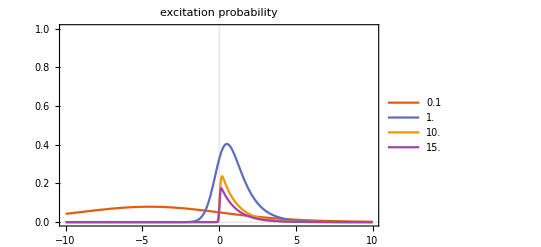

General::munfl: Exp[-5624.54] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12655.2] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

```mathematica
Clear[H,L,t,ρ,rho]
PeArr={};
PulseArr={};
For[i=1,i<Length[Ωarr]+1,i++,
Ω=Ωarr[[i]];

g=√Γp(Ω^2/(2π))^(1/4)Exp[-(Ω (t-t0))^2/4];
AppendTo[PulseArr, g];

(*RWA interaction Hamiltonian-- ignore dc terms for field and atom b.c. there is no detuning here*)
H=I g(-sp.aa+ sm.dag[aa]);

(*decay operator for atom excited state*)
L=√Γ sm;

{eqs,initialConditions, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H, {L}, tmin];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,initialConditions], rho, {t,tmin,tmax}, MaxStepFraction->1/10000]];
Print["Time to run sim step ",i,": ",time];
Pe=soln[[popIdcs[[3]],2]];
AppendTo[PeArr,Pe];
]

Plot[PeArr,{t,tmax-2(tmax-t0),tmax},PlotLegends->Ωarr/Ω0,PlotLabel->"excitation probability",PlotRange->{{tmax-2(tmax-t0),tmax},{0,1}},PlotTheme->"Scientific"]
Plot[PulseArr,{t,tmax-2(tmax-t0),tmax},PlotLegends->Ωarr/Ω0,PlotLabel->"Gaussian pulses",PlotRange->All,PlotTheme->"Scientific"]
```

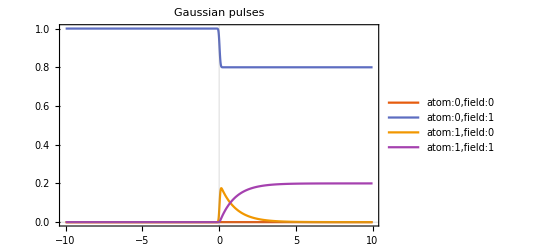

```mathematica
Plot[Evaluate[Array[soln[[popIdcs[[#]],2]]&,4]],{t,tmax-2(tmax-t0),tmax},PlotLegends->{"atom:0,field:0","atom:0,field:1","atom:1,field:0","atom:1,field:1"},PlotLabel->"Gaussian pulses",PlotRange->All,PlotTheme->"Scientific"]
```

```mathematica
L//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0)

```mathematica
{evals,evecs}=Eigensystem[L]
```

{{0,0,0,0},{{0,0,0,1},{0,1,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
Transpose[evecs]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
Transpose[evecs].L.evecs//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
initialConditions
```

{ρ_(1,1)[-100]==0,ρ_(1,2)[-100]==0,ρ_(1,3)[-100]==0,ρ_(1,4)[-100]==0,ρ_(2,2)[-100]==1,ρ_(2,3)[-100]==0,ρ_(2,4)[-100]==0,ρ_(3,3)[-100]==0,ρ_(3,4)[-100]==0,ρ_(4,4)[-100]==0}

```mathematica
H//MatrixForm
```

(0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | (0. +2.99603 I) E^(-126.563 t^2) | 0. +0. I
0. +0. I | (0. -2.99603 I) E^(-126.563 t^2) | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I)

```mathematica
sm//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0)

### account for free energy of the atom, field

In this case, the interaction and Schrodinger picture Hamiltonians are different up to a unitary transformation U = e^(IH_0 t/ℏ) where H0 is the Hamiltonian which contains the energies of the system. This does not change the simulation results that I obtain.

```mathematica
tmin=-100;
tmax=10;
t0=0
(*tmin=0;
tmax=110;
t0=100;*) (*the photon envelope is centered at t0*)

Γ=1;
Γp=Γ;
Ω0=1.5Γ;
Ωarr={0.1,1,10,15}Ω0;

(*basis kets*)
ψatomgfield0=Outer[Times,{1,0},{1,0}];
ψatomgfield1=Outer[Times,{1,0},{0,1}];
ψatomefield0=Outer[Times,{0,1},{1,0}];
ψatomefield1=Outer[Times,{0,1},{0,1}];

(*initial substates, assuming product state input*)
ψ0atom={1,0};(*{g,e}*)
ψ0field={0,1};(*{0,1}*)
ρ0atom=Outer[Times,ψ0atom,ψ0atom];
ρ0field=Outer[Times,ψ0field,ψ0field];
ρ0=KroneckerProduct[ρ0atom,ρ0field];
ρ0//MatrixForm
(*field starts in N=1 state, atom in g*)
```

0

```mathematica
E^(I H0 t)HI E^(-I H0 t)//MatrixForm
```

(0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | (0. +2.99603 I) E^(-126.563 t^2) | 0. +0. I
0. +0. I | (0. -2.99603 I) E^(-126.563 t^2) | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I)

```mathematica
HI//MatrixForm
```

(0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | (0. +2.99603 I) E^(-126.563 t^2) | 0. +0. I
0. +0. I | (0. -2.99603 I) E^(-126.563 t^2) | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I)

```mathematica
Clear[ωa,ωf]
Hatom=ωa/2 σz;
Hfield=ωf/2 σz;
Hatomfield=KroneckerProduct[Hatom,σ0]+KroneckerProduct[σ0,Hfield];
Hatomfield//MatrixForm
ωa=1;
ωf=1;
```

(ωa/2+ωf/2 | 0 | 0 | 0
0 | ωa/2-ωf/2 | 0 | 0
0 | 0 | -ωa/2+ωf/2 | 0
0 | 0 | 0 | -ωa/2-ωf/2)

```mathematica
Clear[H,L,t,ρ,rho]
PeArr={};
PulseArr={};
For[i=1,i<Length[Ωarr]+1,i++,
Ω=Ωarr[[i]];

g=√Γp(Ω^2/(2π))^(1/4)Exp[-(Ω (t-t0))^2/4];
AppendTo[PulseArr, g];

(*RWA interaction Hamiltonian-- ignore dc terms for field and atom b.c. there is no detuning here*)
H0=Hatomfield;
HI=I g(-sp.aa+ sm.dag[aa]);
H=H0+HI;

(*decay operator for atom excited state*)
L=√Γ sm;

{eqs,initialConditions, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H, {L}, tmin];

{time,soln}= Timing[First@NDSolve[Flatten@Join[eqs,initialConditions], rho, {t,tmin,tmax}, MaxStepFraction->1/10000]];
Print["Time to run sim step ",i,": ",time];
Pe=soln[[popIdcs[[3]],2]];
AppendTo[PeArr,Pe];
]

Plot[PeArr,{t,tmax-2(tmax-t0),tmax},PlotLegends->Ωarr/Ω0,PlotLabel->"excitation probability",PlotRange->{{tmax-2(tmax-t0),tmax},{0,1}},PlotTheme->"Scientific"]
Plot[PulseArr,{t,tmax-2(tmax-t0),tmax},PlotLegends->Ωarr/Ω0,PlotLabel->"Gaussian pulses",PlotRange->All,PlotTheme->"Scientific"]
```

Time to run sim step  1 :  0.0625

Time to run sim step  2 :  0.046875

Time to run sim step  3 :  0.078125

Time to run sim step  4 :  0.046875

-Graphics-

General::munfl: Exp[-5624.54] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12655.2] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

```mathematica
Plot[Evaluate[Array[soln[[popIdcs[[#]],2]]&,4]],{t,tmax-2(tmax-t0),tmax},PlotLegends->{"atom:0,field:0","atom:0,field:1","atom:1,field:0","atom:1,field:1"},PlotLabel->"Gaussian pulses",PlotRange->All,PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
H//MatrixForm
```

(1. +0. I | 0. +0. I | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | (0. +2.99603 I) E^(-126.563 t^2) | 0. +0. I
0. +0. I | (0. -2.99603 I) E^(-126.563 t^2) | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | 0. +0. I | -1.+0. I)

```mathematica
ρcollapse
```

{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,0}}

```mathematica
L//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0)

```mathematica
{evals,evecs}=Eigensystem[L]
```

{{0,0,0,0},{{0,0,0,1},{0,1,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
Transpose[evecs]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
Transpose[evecs].L.evecs//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
initialConditions
```

{ρ_(1,1)[-100]==0,ρ_(1,2)[-100]==0,ρ_(1,3)[-100]==0,ρ_(1,4)[-100]==0,ρ_(2,2)[-100]==1,ρ_(2,3)[-100]==0,ρ_(2,4)[-100]==0,ρ_(3,3)[-100]==0,ρ_(3,4)[-100]==0,ρ_(4,4)[-100]==0}

```mathematica
H//MatrixForm
```

(0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | (0. +2.99603 I) E^(-126.563 t^2) | 0. +0. I
0. +0. I | (0. -2.99603 I) E^(-126.563 t^2) | 0. +0. I | 0. +0. I
0. +0. I | 0. +0. I | 0. +0. I | 0. +0. I)

```mathematica
sm//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0)

### testing - compare ρ eqs with s eqs

```mathematica
M=({{-Γ, -2g, -2g}, {0, -Γ/2, 0}, {0, 0, -Γ/2}});
b=({{-Γ}, {-g}, {-g}});
s=({{s1}, {s2}, {s3}});
s0=({{1}, {0}, {0}});
M.s+b//MatrixForm
```

(-2 g s2-2 g s3-Γ-s1 Γ
-g-(s2 Γ)/2
-g-(s3 Γ)/2)

```mathematica
H=I g(-sp.aa+ sm.dag[aa]);
L=√Γ sm;

{eqs,initialConditions, rho,popIdcs,cohIdcs}=BuildMasterEq[ρ0,H, L, tmin];
Refine[eqs,Γ>0]//Simplify//MatrixForm//TraditionalForm
```

(Γ ρ_(1,1)(t)+ρ_(1,1)'(t)==0
Γ ρ_(1,2)(t)+2 ρ_(1,2)'(t)==2 g ρ_(1,3)(t)
g ρ_(1,2)(t)+Γ ρ_(1,3)(t)+ρ_(1,3)'(t)==0
Γ ρ_(1,4)(t)+2 ρ_(1,4)'(t)==0
g Conjugate[ρ_(2,3)(t)]+g ρ_(2,3)(t)+Γ ρ_(1,1)(t)==ρ_(2,2)'(t)
g ρ_(2,2)(t)+1/2 Γ ρ_(2,3)(t)+ρ_(2,3)'(t)==g ρ_(3,3)(t)
g ρ_(3,4)(t)+Γ ρ_(1,3)(t)==ρ_(2,4)'(t)
g Conjugate[ρ_(2,3)(t)]+g ρ_(2,3)(t)+Γ ρ_(3,3)(t)+ρ_(3,3)'(t)==0
2 g ρ_(2,4)(t)+Γ ρ_(3,4)(t)+2 ρ_(3,4)'(t)==0
Γ ρ_(3,3)(t)==ρ_(4,4)'(t))

8 lines of corrupt data deleted.